```mathematica
(*Constants*)
Me = 0.511*10^6;
eleccharge=1.6*10^-19;
c = 299792458;
sigT=6.65*10^-29;
```

```mathematica
(*Cases*)
CBETA150 = {γ->293.54, Elaser->1.17, θ->0,ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6,βIP->1*10^-2,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,θcol->0.5*10^-3,EbSpread->1.6*10^-3,ELSpread->6.57*10^-4};
(*These include the optimised β-θ values*) 
DIANA1020 = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->0.881,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->62.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA680 = {γ->1331, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->0.586,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->93.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA340 = {γ->665, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->0.293,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->187*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
(*σz DIANA is an approximation*)

(*Illya DIANA Version*)
Mine = {γ->665, Elaser->1.207,θ->0,ϵn->0.5*10^-6,ϕ->0,σL->50*10^-6,βIP->0.57,Q->100*10^-12,Epulse->0.1,rep->1,tpulse->5.7*10^-12,σz->1*10^-3,θcol->1.55*10^-4,EbSpread->1.9*10^-3, ELSpread->6.57*10^-4};
Illya ={γ->665, Elaser->1.207,θ->0,ϵn->0.5*10^-6,ϕ->0,σL->50*10^-6,βIP->0.831,Q->100*10^-12,Epulse->0.1,rep->1,tpulse->5.7*10^-12,σz->1*10^-3,θcol->1.39*10^-4,EbSpread->1.9*10^-3, ELSpread->6.57*10^-4};

(*For Plots of (β^*)_IP*)
DIANA1020plot= {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->6*10^-5,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA680plot = {γ->1331, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->6*10^-5,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA340plot = {γ->665, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,θcol->6*10^-5,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
(*For Plots with (β^*)_IP, Subscript[θ, col] as varibales*)
DIANA1020plot3D={γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->1.0,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA680plot3D = {γ->1331, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA340plot3D = {γ->665, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
(* For Plots of Subscript[θ, col]*)
DIANA1020col = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->1.0,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA680col = {γ->1331, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->1.0,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA340col = {γ->665, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->1.0,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
```

```mathematica
(*DIANA 1020MeV Flux against bunch length varying angle*)
DIANA1020σz0 = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,βIP->0.881,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,θcol->62.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA1020σz5 = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->π/36,σL->25*10^-6,βIP->0.881,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,θcol->62.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA1020σz10 = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->π/18,σL->25*10^-6,βIP->0.881,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,θcol->62.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4}; 
DIANA1020σz20 = {γ->1996, Elaser->1.17, θ->0,ϵn->0.5*10^-6,ϕ->π/9,σL->25*10^-6,βIP->0.881,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,θcol->62.7*10^-6,EbSpread->10^-4,ELSpread->6.57*10^-4};
```

```mathematica
(*Recoil Parameter*)
Xrec[γ_,Einc_]:=(4*γ*Einc)/Me;
```

```mathematica
Xrec[γ,Elaser]/.Mine
Xrec[γ,Elaser]/.Illya
```

0.00628301

0.00628301

```mathematica
(*Peak Energy*)
Egam[γ_,Einc_,θ_]:=(4*γ^2*Einc)/(1+(γ*θ)^2+Xrec[γ,Einc]);
Egam[γ,Elaser,θ]/.Mine
Egam[γ,Elaser,θ]/.Illya
```

2.12173×10^6

2.12173×10^6

```mathematica
(*Cross Section - Recoil Correction*)
σ[γ_,Einc_]:=sigT(1-Xrec[γ,Einc]);
σ[γ,Elaser]/.Mine
σ[γ,Elaser]/.Illya
```

6.60822×10^-29

6.60822×10^-29

```mathematica
(*Transverse Beam Spot Size*)
σe[γ_,βIP_,ϵn_]=Sqrt[(βIP*ϵn)/γ];
σe[γ,βIP,ϵn]/.Mine
σe[γ,βIP,ϵn]/.Illya
```

0.000020702

0.0000249962

```mathematica
(*Convolution*)
conv[σL_,γ_,βIP_,ϵn_]:=Sqrt[σe[γ,βIP,ϵn]^2+σL^2];
```

```mathematica
conv[σL,γ,βIP,ϵn]/.CBETA150;
```

```mathematica
convl[σz_,tpulse_]:=Sqrt[σz^2+(c*tpulse)^2];
convl[σz,tpulse]/.CBETA150;
```

```mathematica
(*No. Photons/Electrons*)
NL[Epulse_,Einc_]:=Epulse/(Elaser*eleccharge);
NL[Epulse,Elaser]/.CBETA150;
Ne[Q_]:=Q/eleccharge;
Ne[Q]/.CBETA150;
```

```mathematica
(*Flux per Shot*)
Nγ[Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_]:=σ[γ,Einc](Ne[Q]*NL[Epulse,Einc]*Cos[ϕ/2])/(2*π*conv[σL,γ,βIP,ϵn]*Sqrt[conv[σL,γ,βIP,ϵn]^2*Cos[ϕ/2]^2+convl[σz,tpulse]^2*Sin[ϕ/2]^2])
Nγ[Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.Mine
Nγ[Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.Illya
```

1.16226×10^6

1.08926×10^6

```mathematica
(*Flux per Second*)
F[f_,Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_]:=f*Nγ[Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse];
F[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.CBETA150 ;
F[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.DIANA1020
```

4.10196×10^11

```mathematica
(*Flux in 0.1% Bandwidth*)
F01bw[f_,Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_]:=1.5*10^-3*F[f,Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse];
F01bw[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.CBETA150;
F01bw[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.DIANA1020;
```

```mathematica
(*Flux in any Collimation*)
Fcol[f_,Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_,θcol_]:=F[f,Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse]*((1+CubeRoot[Xrec[γ,Einc]]ψ[γ,θcol]^2/3)ψ[γ,θcol]^2)/((1+(1+Xrec[γ,Einc]/2)ψ[γ,θcol]^2)*(1+ψ[γ,θcol]^2));
Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020
```

(4.10196×10^11 ψ[1996,0.0000627]^2 (1+0.0878093 ψ[1996,0.0000627]^2))/((1+ψ[1996,0.0000627]^2) (1+1.00914 ψ[1996,0.0000627]^2))

```mathematica
(*Average Brilliance*)
B01bwAvg[γ_,f_,Q_,Epulse_,σL_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_]:=(γ^2*F01bw[f,Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse])/(4*π^2*(ϵn*10^6)^2);
B01bwAvg[γ,rep,Q,Epulse,σL,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.CBETA150;
B01bwAvg[γ,rep,Q,Epulse,σL,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.DIANA1020
```

2.48373×10^14

```mathematica
(*Peak Brilliance*)
B01bwPk[Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_]:=1.5*10^-3*(γ^2*Nγ[Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse])/(4*π^2*(ϵn*10^6)^2*tpulse);
B01bwPk[Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.Mine
B01bwPk[Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse]/.Illya
```

1.37044×10^19

1.28438×10^19

```mathematica
(*Collimation Angle*)
ψ[γ_,θcol_]:=γ*θcol;
ψ[γ,θcol]/.CBETA150;
ψ[γ,θcol]/.DIANA1020;
```

```mathematica
(*Collimation Term*)
collterm[γ_,θcol_,Einc_]:=1/Sqrt[12]*ψ[γ,θcol]^2/(1+Xrec[γ,Einc]+ψ[γ,θcol]^2/2);
collterm[γ,θcol,Elaser]/.CBETA150;
collterm[γ,θcol,Elaser]/.DIANA1020
```

0.00440627

```mathematica
(*Beam Energy Spread Term*)
BeamEterm[γ_,Einc_,θcol_,EbSpread_]:=(2+Xrec[γ,Einc])/(1+Xrec[γ,Einc]+ψ[γ,θcol]^2)*EbSpread;
BeamEterm[γ,Elaser,θcol,EbSpread]/.CBETA150;
BeamEterm[γ,Elaser,θcol,EbSpread]/.DIANA1020
```

0.000195202

```mathematica
(*Laser Energy Spread Term*)
LaserEterm[γ_,θcol_,Einc_,ELSpread_]:=(1+ψ[γ,θcol]^2)/(1+Xrec[γ,Einc]+ψ[γ,θcol]^2)*ELSpread;
LaserEterm[γ,θcol,Elaser,ELSpread]/.CBETA150;
LaserEterm[γ,θcol,Elaser,ELSpread]/.DIANA1020
```

0.000645384

```mathematica
(*Emittance Term*)
emitterm[γ_,ϵn_,βIP_]:=(2*γ*ϵn)/βIP;
emitterm[γ,ϵn,βIP]/.CBETA150;
emitterm[γ,ϵn,βIP]/.DIANA1020
```

0.00226561

```mathematica
(*Bandwidth*)
BW[γ_,θcol_,Einc_,EbSpread_,ELSpread_,ϵn_,βIP_]:=Sqrt[collterm[γ,θcol,Einc]^2+BeamEterm[γ,Einc,θcol,EbSpread]^2+LaserEterm[γ,θcol,Einc,ELSpread]^2+emitterm[γ,ϵn,βIP]^2]*100;
BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.Mine
BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.Illya
```

0.500313

0.45971

```mathematica
(*Spectral Energy Density*)
SpecDen01[f_,Q_,Epulse_,σL_,γ_,βIP_,ϵn_,Einc_,ϕ_,σz_,tpulse_,θcol_,EbSpread_,ELSpread_]:=(F01bw[f,Q,Epulse,σL,γ,βIP,ϵn,Einc,ϕ,σz,tpulse]*100)/(4*Sqrt[2*π]*γ^2*Einc*BW[γ,θcol,Einc,EbSpread,ELSpread,ϵn,βIP]);
(*Factor of 100 is as bandwidth has this so value is given in %*) 
SpecDen[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol,EbSpread,ELSpread]/.Mine
SpecDen[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol,EbSpread,ELSpread]/.Illya
```

43.4069

44.274

```mathematica
(*Flux and Bandwidth surface plots vs θcol, (β^*)_IP*)
(*Remember to Quit Kernel + Evaluate Notebook Again to get these Plots*)
Plot3D[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA680plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA340plot3D},{θcol,10^-6,10^-4},{βIP,0.1,5},AxesLabel->{"Collimation Angle (rad)","Beta Function at the IP β_IP (m)","Flux (ph/s)"},PerformanceGoal->"Quality",PlotPoints->100]
```

-Graphics3D-

```mathematica
Plot3D[{BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA1020plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA680plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA340plot3D},{θcol,10^-6,10^-4},{βIP,0.01,5},AxesLabel->{"Collimation Angle (rad)","Beta Function at the IP β_IP (m)", "Bandwidth (%)"}]
```

-Graphics3D-

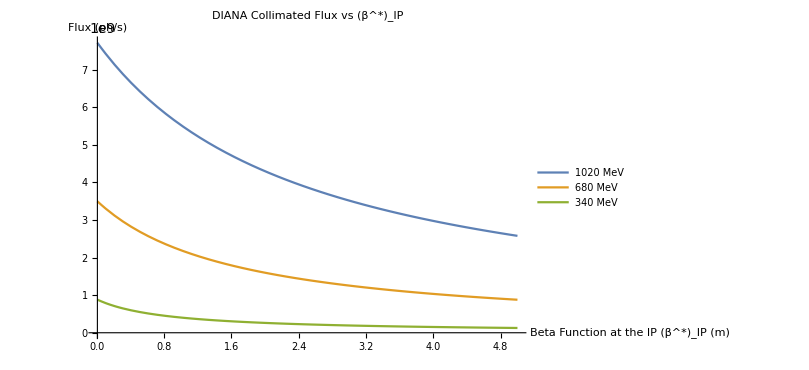

```mathematica
(*DIANA 3 Pass Collimated Flux vs (β^*)_IP Plot*)
Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020plot,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA680plot, Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA340plot},{βIP,0.01,5},PlotLabel->"DIANA Collimated Flux vs (β^*)_IP",AxesLabel->{"Beta Function at the IP (β^*)_IP (m)","Flux (ph/s)"},PlotLegends->Placed[{"1020 MeV","680 MeV","340 MeV"},{0.85,0.7}]]
```

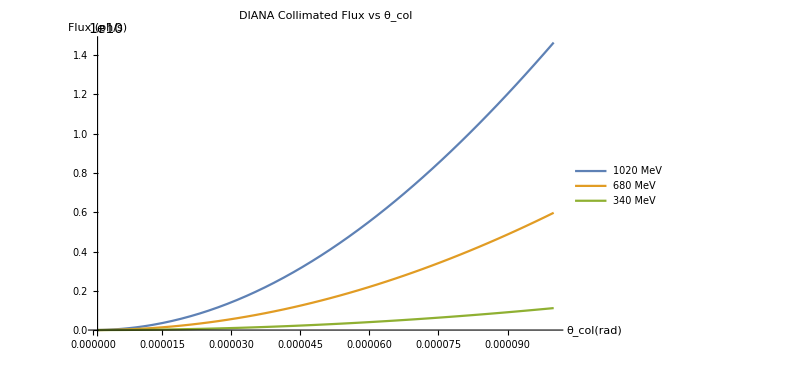

```mathematica
(*DIANA 3 Pass Collimated Flux vs Subscript[θ, col] Plot*)
Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020col,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA680col, Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA340col},{θcol,10^-6,10^-4},PlotLabel->"DIANA Collimated Flux vs θ_col",AxesLabel->{"θ_col(rad)","Flux (ph/s)"},PlotLegends->Placed[{"1020 MeV","680 MeV","340 MeV"},{0.55,0.85}]]
```

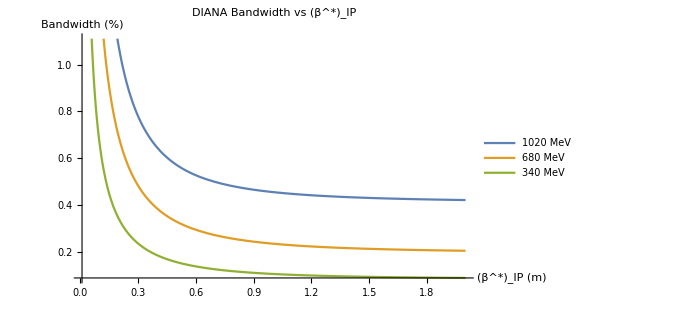

```mathematica
(*DIANA 3 Pass Bandwidth vs  (β^*)_IP Plot*)
Plot[{BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA1020plot,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA680plot,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA340plot},{βIP,0.01,2},PlotLabel->"DIANA Bandwidth vs (β^*)_IP",AxesLabel->{"(β^*)_IP (m)","Bandwidth (%)"},PlotLegends->Placed[{"1020 MeV","680 MeV","340 MeV"},{0.85,0.7}]]
```

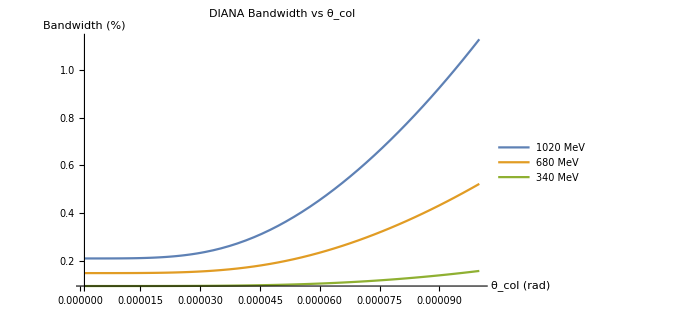

```mathematica
(*DIANA 3 Pass Bandwidth vs Subscript[θ, col] Plot*)
Plot[{BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA1020col,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA680col,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA340col},{θcol,10^-6,10^-4},PlotLabel->"DIANA Bandwidth vs θ_col",AxesLabel->{"θ_col (rad)","Bandwidth (%)"},PlotLegends->Placed[{"1020 MeV","680 MeV","340 MeV"},{0.55,0.85}]]
```

```mathematica
(*Bandwidth and Collimated Flux Manipulate*)
Manipulate[GraphicsGrid[{{Plot[{BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA1020plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA680plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA340plot3D},{βIP,0.01,5},PlotLabel->"Bandwidth vs (β^*)_IP",AxesLabel->{"(β^*)_IP (m)","Bandwidth (%)"}],Plot[{BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA1020plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA680plot3D,BW[γ,θcol,Elaser,EbSpread,ELSpread,ϵn,βIP]/.DIANA340plot3D},{θcol,10^-6,10^-4},PlotLabel->"Bandwidth vs θ_col",AxesLabel->{"θ_col (rad)","Bandwidth (%)"}]},{Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA680plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA340plot3D},{βIP,0.01,5},PlotLabel->"Collimated Flux vs (β^*)_IP",AxesLabel->{"(β^*)_IP (m)","Collimated Flux (ph/s)"}],Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA680plot3D,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA340plot3D},{θcol,10^-6,10^-4},PlotLabel->"Collimated Flux vs θ_col",AxesLabel->{"θ_col (rad)","Flux (ph/s)"}]}}],{{θcol,6*10^-5},10^-6,10^-4},{{βIP,1},0.5,5}]
```

ReplaceAll::reps: {DIANA1020plot3D} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {DIANA1020plot3D} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

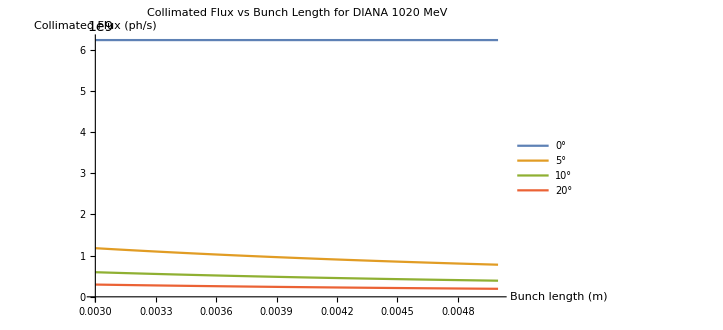

```mathematica
(*3D Plot of Crossing Angle and Bunch Length*)
Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz0,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz5,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz10,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz20},{σz,3*10^-3,5*10^-3},PlotLabel->"Collimated Flux vs Bunch Length for DIANA 1020 MeV",AxesLabel->{"Bunch length (m)","Collimated Flux (ph/s)"},PerformanceGoal->"Quality",PlotPoints->100,PlotLegends->Placed[{"0°","5°","10°","20°"},{0.75,0.7}]]
```

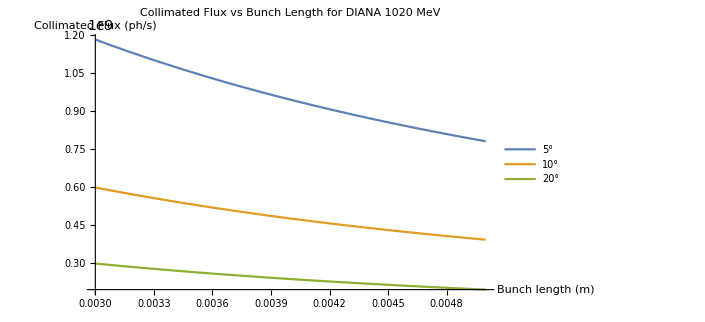

```mathematica
Plot[{Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz5,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz10,Fcol[rep,Q,Epulse,σL,γ,βIP,ϵn,Elaser,ϕ,σz,tpulse,θcol]/.DIANA1020σz20},{σz,3*10^-3,5*10^-3},PlotLabel->"Collimated Flux vs Bunch Length for DIANA 1020 MeV",AxesLabel->{"Bunch length (m)","Collimated Flux (ph/s)"},PerformanceGoal->"Quality",PlotPoints->100,PlotLegends->Placed[{"5°","10°","20°"},{0.75,0.83}]]
```